```mathematica
s={Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]};
ParametricPlot3D[s,{u,0,2π},{v,0,π}]
```

-Graphics3D-

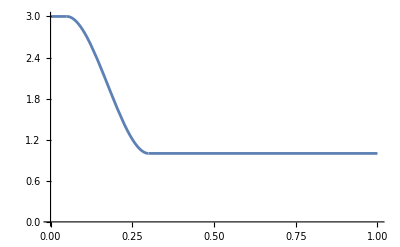

```mathematica
smoothStep[a_,b_,x_]:=With[{t=Clip[(x-a)/(b-a),{0,1}]},-2 t^3+3 t^2]
f[x_]:=2 smoothStep[0.3,0.05,x]+1
Plot[f[x],{x,0,1},PlotRange->{0,3}]
```

```mathematica
pts=SpherePoints[12];
dis[p_]:=Min[Norm[p-#]&/@pts]
ParametricPlot3D[s f[dis[s]],{u,0,2π},{v,0,π},(*Mesh->None,*)PlotPoints->50]
```

-Graphics3D-

### 整理

```mathematica
s={Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]};m[a_,b_,x_]:=-2t^3+3t^2/.t->Clip[(x-a)/(b-a),{0,1}];o=SpherePoints[12];d[p_]:=Min[Norm[p-#]&/@o];ParametricPlot3D[s(3m[.35,.01,d[s]]+1),{u,0,2Pi},{v,0,Pi},Mesh->None,PlotPoints->90,PlotStyle->MaterialShading["Glazed"],PlotTheme->{"NoAxes","Web"}]
```

-Graphics3D-

```mathematica
Manipulate[Plot[Exp[-x^2/a^2],{x,0,1},PlotRange->{0,1}],{{a,1},0.001,3}]
```

```mathematica
ParametricPlot3D[s(3Exp[-d[s]^2/0.04^2]+1),{u,0,2Pi},{v,0,Pi},Mesh->None,PlotPoints->30,PlotTheme->{"NoAxes","Web"}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[s(m[.35,.01,d[s]]+1),{u,0,2Pi},{v,0,Pi},Mesh->None,PlotPoints->50,PlotTheme->{"NoAxes","Web"}]
```

-Graphics3D-

```mathematica
smoothStep[n_,x_]:=-n t^(n+1)+(n+1)t^n/.t->Clip[(x-0)/(1-0),{0,1}];
Manipulate[
Plot[{x,x^n,smoothStep[n,x]},{x,-2,2},PlotRange->{-1,1}],{{n,2},0,8} ]
```

```mathematica
ParametricPlot3D[s(m[.3,.01,d[s]^0.7]+1),{u,0,2Pi},{v,0,Pi},Mesh->None,PlotPoints->80,PlotTheme->{"NoAxes","Web"}]
```

-Graphics3D-